```mathematica
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
```

unitfat::shdw: Symbol "unitfat" appears in multiple contexts {"PenroseTilingFunctions`", "Global`"}; definitions in context "PenroseTilingFunctions`" may shadow or be shadowed by other definitions.

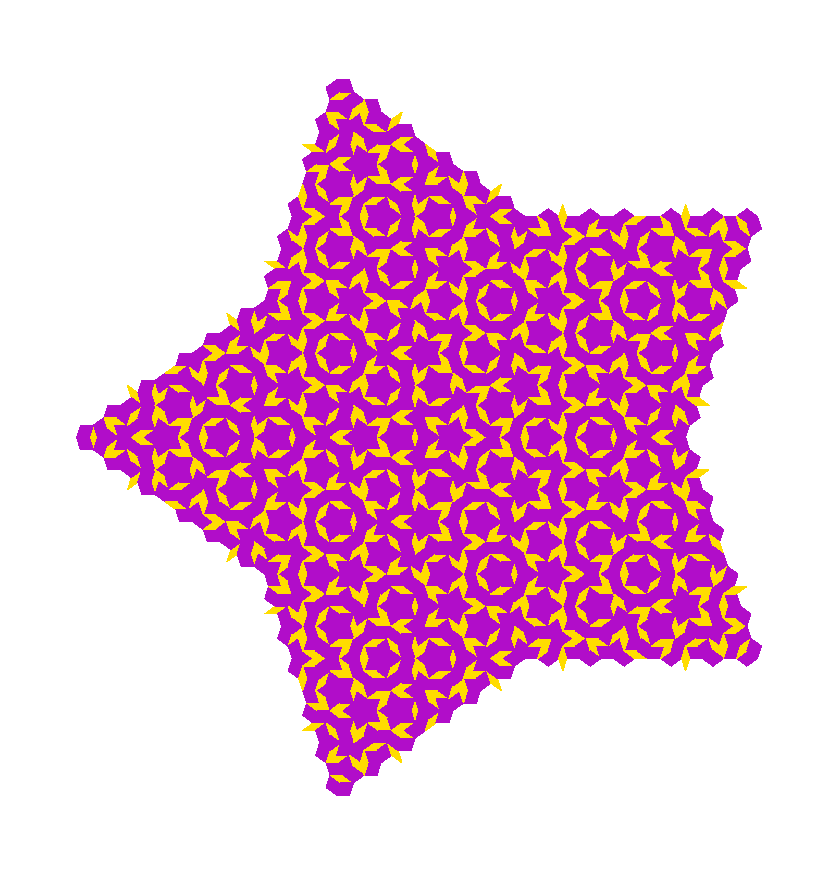

```mathematica
See@FullInflate[starseed,6]
```

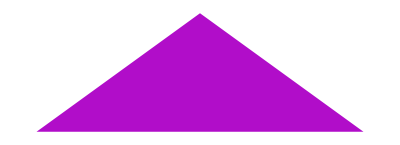

```mathematica
See@{unitfat}
```

```mathematica
Coor/@Δ/@{unitfat}
```

{{{-0.809017,0},{0.809017,0},{1.11022×10^-16,0.587785}}}

```mathematica
Graphics[Line[{{-0.8090169943749475,0},{0.8090169943749475,0}}]]
```

```mathematica
Kites[{{A_,B_,C_},t_}]:=
If[t=="fat",Line[Coor[{A,B}]],Line[Coor[{B,C}]]]
```

```mathematica
{unitfat}
```

{{{-0.809017,0.809017,1.11022×10^-16+0.587785 ⅈ},fat}}

```mathematica
Coor[{-0.8090169943749475,0.8090169943749475}]
```

{{-0.809017,0},{0.809017,0}}

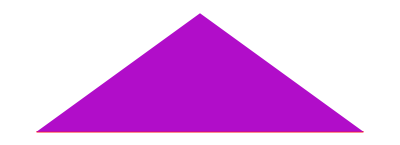

```mathematica
Show[Graphics[{Thick,Red,Kites[unitfat]}],See@{unitfat}]
```

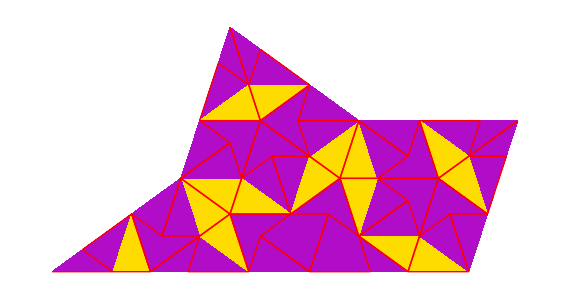

```mathematica
Show[See@Inflate[starseed,2],Graphics[{Red,Thick,Kites/@Inflate[starseed,3]}]]
```

```mathematica
KiteFill[{{A_,B_,C_},t_}]:=If[t=="fat",{{A,C,A+(A-B)(1-ϕ)},{B,C,A+(A-B)(1-ϕ)}},None]
SeeKitesDatrts[list_]:= Graphics[Triangle/@Coor/@Flatten[KiteFill/@list,1]]
```

{{{-0.809017,1.11022×10^-16+0.587785 ⅈ,0.190983},{0.809017,1.11022×10^-16+0.587785 ⅈ,0.190983}}}

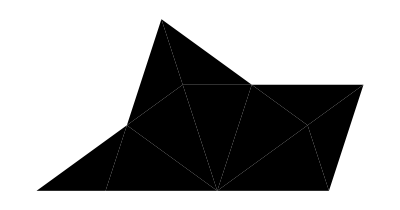

```mathematica
KiteFill/@{unitfat}
Graphics[Triangle/@Coor/@Flatten[KiteFill/@starseed,1]]
```

```mathematica
Show[{See@{unitfat},Graphics[Triangle/@Flatten[KiteFill/@{unitfat},1]]}]
```

-Graphics-

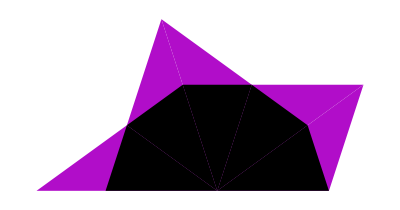

```mathematica
Show[{See@starseed,Graphics[Triangle/@Coor/@KiteFill/@starseed]}]
```

```mathematica
??FatInflate
```

Inflation Rules for fat triangles

FatInflate[{{a_,b_,c_},f_}]:=Block[{d=a+(c-a)/ϕ,e=a+(b-a)/ϕ},{Fat[{e,a,d}],Skinny[{d,c,e}],Fat[{b,c,e}]}]

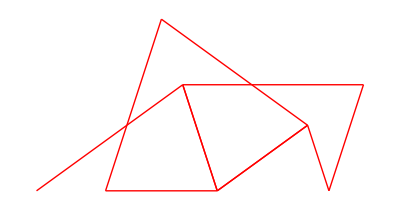

```mathematica
Graphics[{Red,Thick,Kites/@Inflate[starseed,1]}]
```

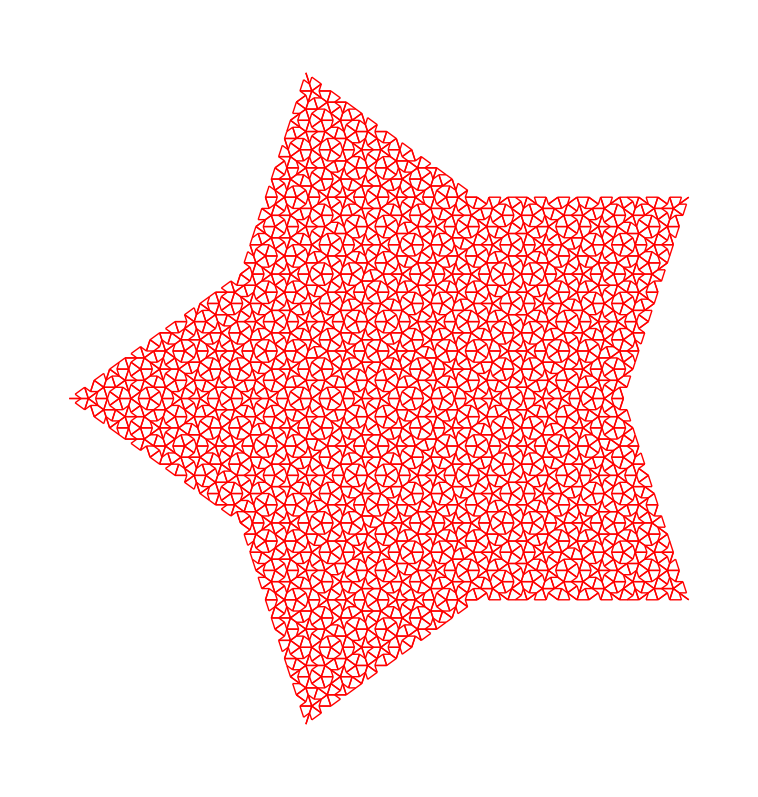

```mathematica
Graphics[{Red,Thick,Kites/@AddConj[Inflate[starseed,7]]}]
```

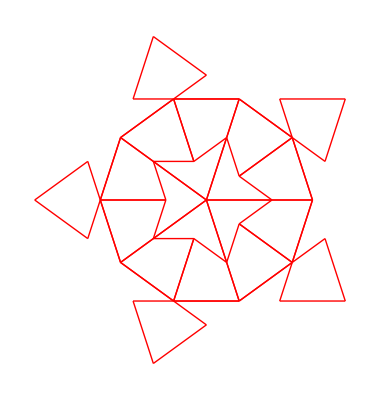
```mathematica
-Graphics-3
```

3 -Graphics-

```mathematica
??FullInflate
```

Inflates, Conjugates, Culls, and Converts to Rhombs

FullInflate[seed_,n_]:=Rhomb/@Cull[AddConj[Inflate[seed,n]]]

```mathematica
unitfat
```

{{-0.809017,0.809017,1.11022×10^-16+0.587785 ⅈ},fat}

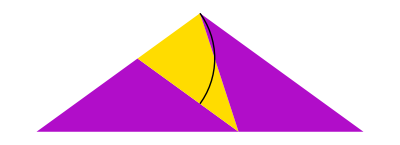

```mathematica
Show[See@Inflate[{unitfat},1],Graphics@Circle[{-0.30901699437494745,0.3632712640026805},ϕ/(2ϕ+1),{-0.6283185307179588,0.6283185307179585}]]
```

```mathematica
unitfat
```

{{-0.809017,0.809017,1.11022×10^-16+0.587785 ⅈ},fat}

```mathematica
1.1102230246251565*^-16+0.5877852522924732 ⅈ-(-0.8090169943749475)
```

0.809017+0.587785 ⅈ

```mathematica
Arg[0.8090169943749476+0.5877852522924732 ⅈ]
```

0.628319

```mathematica
0.6283185307179586*57
```

35.8142

```mathematica
{-0.30901699437494745+0.3632712640026805 ⅈ,1.1102230246251565*^-16+0.5877852522924732 ⅈ,0.19098300562505244}
```

```mathematica
Coor@{-0.30901699437494745+0.3632712640026805 ⅈ,1.1102230246251565*^-16+0.5877852522924732 ⅈ,0.19098300562505244}
```

{{-0.309017,0.363271},{1.11022×10^-16,0.587785},{0.190983,0}}

```mathematica
0.19098300562505244-(-0.30901699437494745+0.3632712640026805 ⅈ)
```

0.5-0.363271 ⅈ

```mathematica
1.1102230246251565*^-16+0.5877852522924732 ⅈ-(-0.30901699437494745+0.3632712640026805 ⅈ)
```

0.309017+0.224514 ⅈ

```mathematica
Arg[0.30901699437494756+0.22451398828979274 ⅈ]
```

0.628319

```mathematica
0.19098300562505244-(1.1102230246251565*^-16+0.5877852522924732 ⅈ)
```

0.190983-0.587785 ⅈ

```mathematica
Arg[0.19098300562505233-0.5877852522924732 ⅈ]
```

-1.25664

```mathematica
Arg[0.4999999999999999-0.3632712640026805 ⅈ]
```

-0.628319

```mathematica
-0.6283185307179588*57
```

-35.8142

```mathematica
Circle[{-0.30901699437494745,0.3632712640026805}]
```

Circle[{-0.309017,0.363271}]

Transpose::nmtx: The first two levels of {-0.309017 + 0.363271\ ⅈ, -0.309017 + 0.363271\ ⅈ} cannot be transposed.

Transpose[{-0.309017+0.363271 ⅈ,-0.309017+0.363271 ⅈ}]

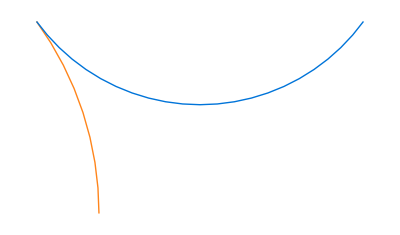

```mathematica
MakeCurveRules[{{A_,B_,C_},t_}]:=Module[
{aclength=Abs[C-A],
coors=Coor@{A,B,C},
sideθ1=Arg[B-A],
sideθ2=Arg[C-A],
topθ1=Arg[A-C],
topθ2=Arg[B-C]},
sideradius=aclength/ϕ;
topradius=(1-1/ϕ)aclength;
coorA=coors[[1]];
coorB=coors[[2]];
coorC=coors[[3]];
If[t=="fat",
{{Thick,NiceOrange,Circle[coorA,sideradius,{sideθ1,sideθ2}]},{Thick,NiceBlue,Circle[coorC,topradius,{topθ1,topθ2}]}},
{{Thick,NiceBlue,Circle[coorA,topradius,{sideθ1,sideθ2}]},{Thick,NiceOrange,Circle[coorC,sideradius,{topθ1,topθ2}]}}]]
```

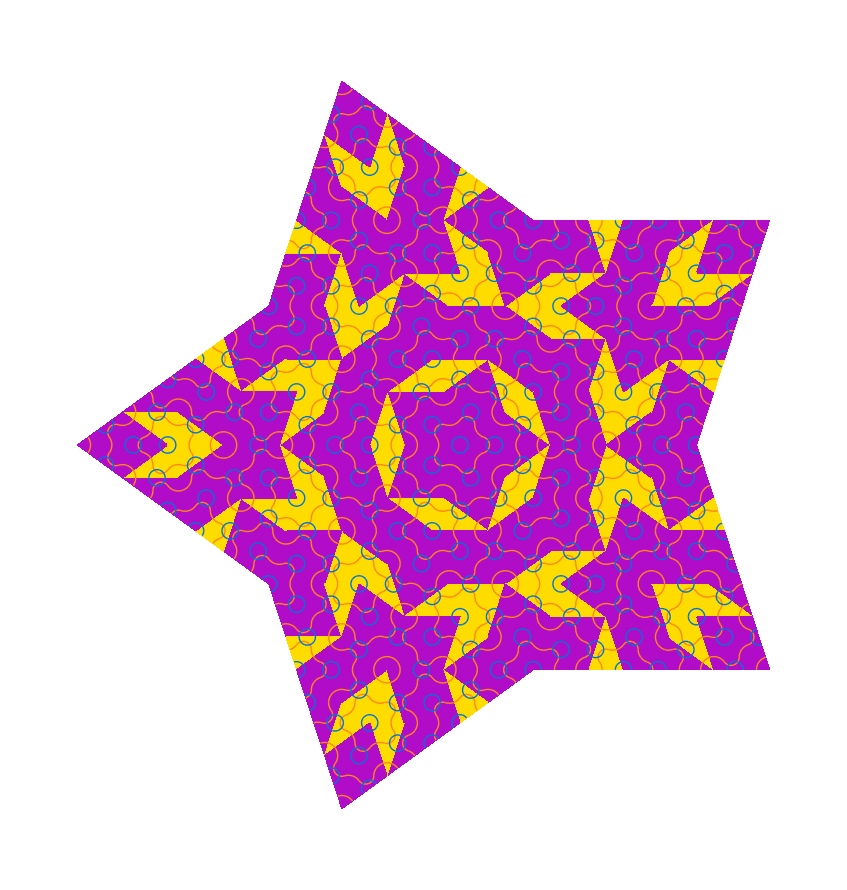

```mathematica
Show[See@Inflate[AddConj@starseed,3],Graphics[MakeCurveRules/@Inflate[AddConj@starseed,5]]]
```

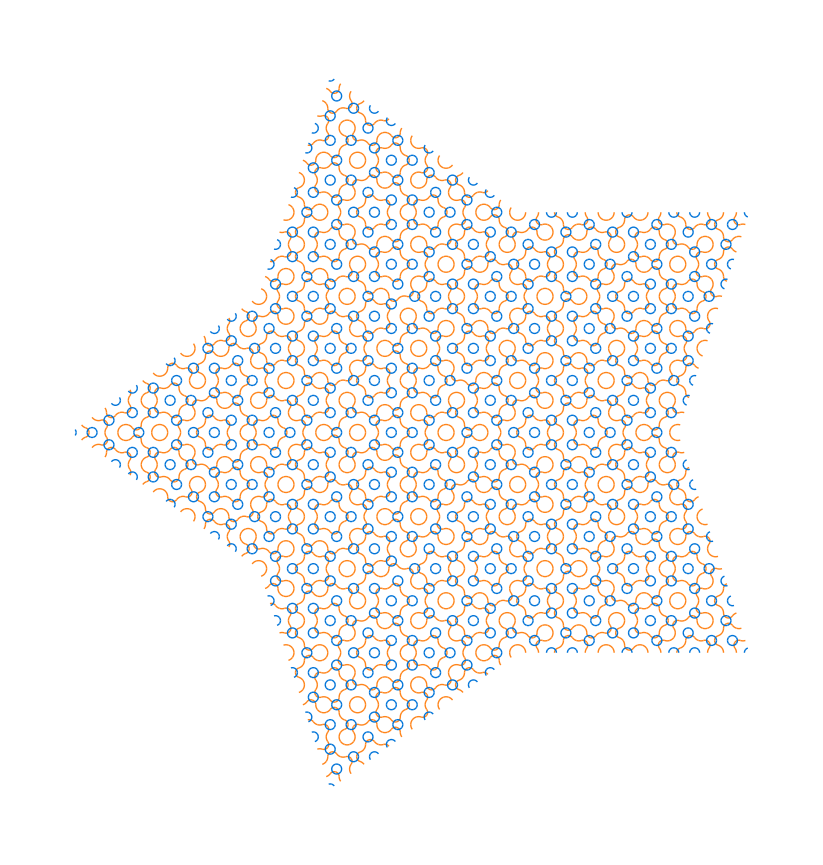

False

```mathematica
Graphics[MakeCurveRules/@Inflate[AddConj@starseed,6]]
```

```mathematica
arctest[θ_,α_]:=If[θ<α,Graphics@{Circle[{0,0},1,{θ,α}]},Graphics@Circle[{0,0},1,{2Pi+α,θ}]]
```

```mathematica
AngleTest[{θ_,α_}]:=If[θ<α,True,False]
```

```mathematica
CCW[{θ_,α_}]:=If[θ<α,{θ,α},{θ,α+2Pi}]
CW[{θ_,α_}]:=If[θ<α,{α,θ+2Pi},{α,θ}]
```

```mathematica
arctest[5Pi/4,3Pi/4];
```

```mathematica
AngleSweep@{5Pi/4,3Pi/4}
```

{(11 π)/4,(5 π)/4}

```mathematica
MakeCurveRules[{{A_,B_,C_},t_}]:=Module[
{coors=Coor@{A,B,C},
littlelength=If[t=="fat",Abs[C-A],Abs[B-C]],
biglength=If[t=="fat",Abs[B-A],Abs[C-A]],
Aθ1=Arg[B-A],
Aθ2=Arg[C-A],
Bθ1=Arg[A-B],
Bθ2=Arg[C-B]},
littleradius=littlelength/(1+ϕ);
bigradius=littlelength-littleradius;

coorA=coors[[1]];
coorB=coors[[2]];
coorC=coors[[3]];
orientation=Sign@Det[Transpose@{(coorA-coorB),(coorC-coorB)}];

{Aθ1,Aθ2}=If[orientation==1,
CW[#],
CCW[#]]&@{Aθ1,Aθ2};

{Bθ1,Bθ2}=If[orientation==1,
CCW[#],
CW[#]]&@{Bθ1,Bθ2};

Color1=NiceOrange;
Color2=NiceBlue;

If[t=="fat",
{{Thick,Color1,Circle[coorA,bigradius,{Aθ1,Aθ2}]},{Thick,Color2,Circle[coorB,littleradius,{Bθ1,Bθ2}]}},
{{Thick, Color1,Circle[coorA,littleradius,{Aθ1,Aθ2}]},{Thick,Color2,Circle[coorB,littleradius,{Bθ1,Bθ2}]}}]]
```

```mathematica
{t1,t2}={1,2}
```

{1,2}

```mathematica
t1
```

1

```mathematica
t2
```

2

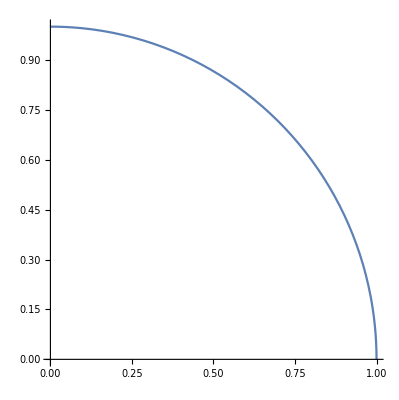

```mathematica
PolarPlot[1,{r,Pi/2,0}]
```

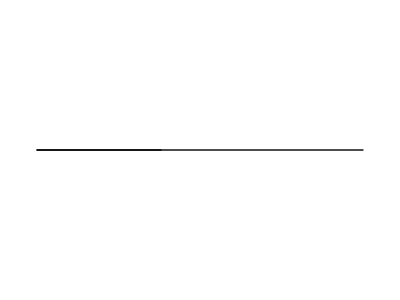

```mathematica
Show[Graphics[Line[{{0,0},{1,0}}]],Graphics[Line[{{0,0},{1/(1+ϕ),0}}]]]
```